# Laser Cooling Rb

#### Constants

```mathematica
c= 2.9987*10^8; (*[m/s]*)
h  = 6.626*10^-34;(*[J s]*)
ℏ = h/(2 π);
kB = 1.3807*10^-23;(*[J/K]*)
mRb = 1.4192261*10^-25; (*[kg]*)
λD2 = 7.8*10^-7; (*[m]*)
γD2 = 2π 6.0659*10^6 ;(*[rad Hz]*)
ωD2 = 2 π * c/λD2
```

2.41556×10^15

```mathematica
2.415562535979414*^15/(2 π)
```

3.84449×10^14

```mathematica
ΔMOT = - 2 γD2; 
ΔPGC = - 5 γD2;γMOT = 2 π * 6*10^-6 ;(*linewidth of MOT beam [Hz]; might actually be more narrow than this by ~1 MHz*)
```

```mathematica
TD= (h ΓD2)/(2 π *2kB)/10^-6
```

145.626

```mathematica
k = 2 π/(7.8*10^-7);
```

```mathematica
TR = ((h/(2π))^2 k^2)/(kB * 1.419226*^-25)
```

3.68454×10^-7

```mathematica
1.4192261×10^-25
```

1.41923×10^-25

```mathematica
37*9*10^-27//N
```

3.33×10^-25

#### Atom escape times

Suppose an atom has some temperature T, in a trap of radius w0? What is the shortest time it will take the atom to move outside of the beam cross-section (perpendicular to the optical axis) if the beam is turned off instantaneously?

```mathematica
vRMS[T_]:= √((2 kB T)/mRb);  w0 = 2.5*10^-6;
```

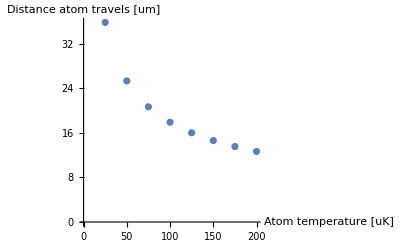

```mathematica
ListPlot[Table[{T/10^-6,w0/(vRMS[T]*10^-6)},{T,Range[25*10^-6,200*10^-6,25*10^-6]}],AxesLabel-> {"Atom temperature [uK]","Distance atom travels [um]"}]
```

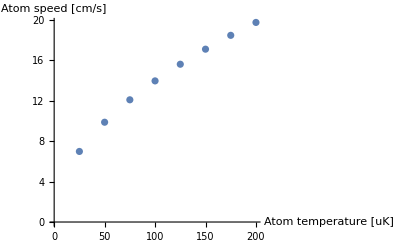

```mathematica
ListPlot[Table[{T/10^-6,vRMS[T]*100},{T,Range[25*10^-6,200*10^-6,25*10^-6]}],AxesLabel-> {"Atom temperature [uK]","Atom speed [cm/s]"}]
```

#### SWAP Cooling

Need frequency range swept > 2kv

```mathematica
v = 0.1; (*[m/s]*)
kD2 = (2 π)/λD2
```

8.05537×10^6

```mathematica
ωAmplitude = kD2 v (*the minimum amplitude for the cooling frequency modulation*)
```

805537.

#### MOT Radiative Forces

```mathematica
Is = g1/g2(ℏ γD2 ωD2^3)/(12 π c^2) ;g1 = 5; g2 = 7;(*saturation intensity. gi = ith state degeneracy*)
```

```mathematica
β[Δ_,I_]:=8ℏ kD2^2(-Δ/γD2)/((1+4 Δ^2/γD2^2)^2)I/Is;(*s set to 1*)
F[Δ_,I_]:= (ℏ kD2 γD2)/2 I/Is 1/(1+(4 Δ^2)/γD2^2+I/Is);
```

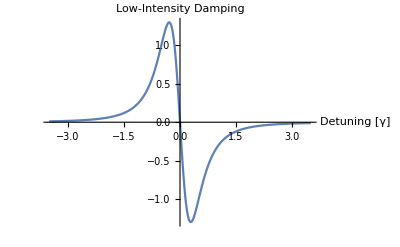

```mathematica
Plot[β[Δ*γD2,Is]/(ℏ kD2^2),{Δ,-3.5,3.5},PlotRange-> Full,AxesLabel->{"Detuning [γ]","Low-Intensity Damping"}]
```

MOT intensity per arm:

```mathematica
IMOT = (5*10^-4)/(π (.005)^2) ;(*Assumes 1mm wide circular beams, ~.5mW*)
```

An atom in our FORT during RO is exposed to the MOT light for ~ (1-.53)*8*10^-7 s

```mathematica
d=.53
```

0.53

```mathematica
tFree =(1-d)*8*10^-7;
fChop= 1.25*10^6;
tRO = 2*10^-3;(*5*10^-3;*)
tTotal= tFree*fChop*tRO
```

0.00094

Consider two beams of a MOT with differing intensities.

```mathematica
FNet[I1_,I2_] := F[-3 γD2,I1]-F[-3 γD2,I2];
```

```mathematica
Clear[t]
```

```mathematica
Manipulate[Plot[(1/2 FNet[α s,.9 α*s]/mRb ((1-duty)*8*10^-7)^2)/10^-6,{α,.1,1},AxesLabel->{"I_Rel","Distance traveled"}],{duty,.3,.8}]
```

#### Random Stuff

Can I spatially separate out the sideband components of the Raman?

```mathematica
νD2 = ωD2/(2 π)
```

3.84449×10^14

```mathematica
λD2HF = c/(νD2 + 6.8*10^9)
```

```mathematica
7.799862038655905*^-7
```

Diffraction off a cd:

```mathematica
d = 1.6*10^-6;
```

```mathematica
ArcSin[λD2/(2*d)]*180/π
```

14.108

```mathematica
ArcSin[λD2HF/(2*d)]*180/π
```

14.1077

Angles for diffraction of the two frequency components of the Raman light occur less than a thousandth of a degree apart... maybe I could resolve this if I got far enough away. 
Diffraction off of a blue ray ?

```mathematica
d = .8*10^-6;
```

```mathematica
ArcSin[λD2/(2*d)]*180/π
```

29.1764

```mathematica
ArcSin[λD2HF/(2*d)]*180/π
```

29.1758

```mathematica
d = .4*10^-6;(*the smaller the d, the more resolution*)
```

```mathematica
ArcSin[λD2/(2*d)]*180/π
```

77.1614

```mathematica
ArcSin[λD2HF/(2*d)]*180/π
```

77.157